```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
<<RLBot`
SetDirectory[NotebookDirectory[]];
```

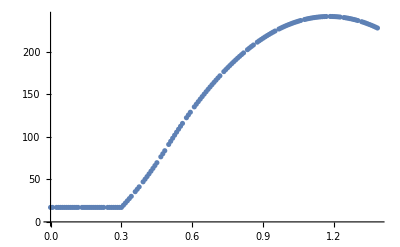

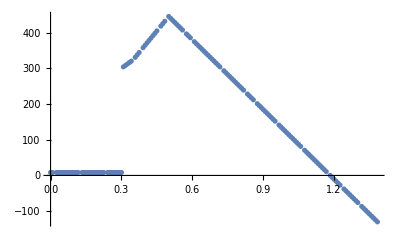

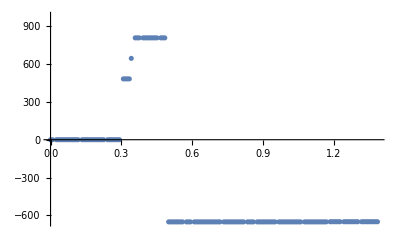

```mathematica
{frame, ball, inputs, car} = ImportPhysicsTickJSONEpisode["jump.json"];
frame = frame-frame[[1]];
t = frame * 1/120.0;
x = #["location"][[3]] & /@ car;
v = #["velocity"][[3]] & /@ car;
a = (v[[2;;-1]] - v[[1;;-2]])/(t[[2;;-1]] - t[[1;;-2]]);

ListPlot[Transpose[{t[[1;;150]], x[[1;;150]]}]]
ListPlot[Transpose[{t[[1;;150]], v[[1;;150]]}]]
ListPlot[Transpose[{t[[1;;150]], a[[1;;150]]}]]
```

```mathematica
data = ImportString[
"0.008333000354468822,19.395326614379883,286.25054931640625
0.016666000708937645,21.836782455444336,292.98638916015625
0.024999000132083893,24.334367752075195,299.72222900390625
0.03333200141787529,26.88808250427246,306.45806884765625
0.04166500270366669,29.497926712036133,313.19390869140625
0.049998003989458084,32.163902282714844,319.92974853515625
0.05833100527524948,34.88600540161133,326.66558837890625
0.06666400283575058,37.66423797607422,333.40142822265625
0.07499700039625168,40.49860382080078,340.13726806640625
0.08332999795675278,43.38909912109375,346.87310791015625
0.09166299551725388,46.335723876953125,353.60894775390625
0.09999599307775497,49.338478088378906,360.34478759765625
0.10832899063825607,52.397361755371094,367.08062744140625
0.11666198819875717,55.51237487792969,373.81646728515625
0.12499498575925827,58.68351745605469,380.55230712890625
0.13332799077033997,61.910789489746094,387.28814697265625
0.14166098833084106,65.1941909790039,394.02398681640625
0.14999398589134216,68.53372192382812,400.75982666015625
0.15832698345184326,71.92938232421875,407.49566650390625
0.16665998101234436,75.38117218017578,414.23150634765625
0.17499297857284546,78.88909149169922,420.96734619140625
0.18332597613334656,82.45314025878906,427.70318603515625
0.19165897369384766,86.07331848144531,434.43902587890625
0.19999197125434875,89.74962615966797,441.17486572265625
0.20832496881484985,93.48206329345703,447.91070556640625
0.21665796637535095,97.16936492919922,442.4942626953125
0.22499096393585205,100.81153106689453,437.07781982421875
0.23332396149635315,104.4085693359375,431.661376953125
0.24165695905685425,107.9604721069336,426.24493408203125
0.24998995661735535,111.46723937988281,420.8284912109375
0.25832295417785645,114.92887115478516,415.41204833984375
0.26665595173835754,118.34536743164062,409.99560546875
0.27498894929885864,121.71672821044922,404.57916259765625
0.28332194685935974,125.04295349121094,399.1627197265625
0.29165494441986084,128.32403564453125,393.74627685546875
0.29998794198036194,131.5599822998047,388.329833984375
0.30832093954086304,134.75079345703125,382.91339111328125
0.31665393710136414,137.89646911621094,377.4969482421875
0.32498693466186523,140.99700927734375,372.08050537109375
0.33331993222236633,144.0524139404297,366.6640625
0.34165292978286743,147.06268310546875,361.24761962890625
0.34998592734336853,150.02783203125,355.8311767578125
0.35831892490386963,152.94784545898438,350.41473388671875
0.3666519224643707,155.82272338867188,344.998291015625
0.3749849200248718,158.6524658203125,339.58184814453125
0.3833179175853729,161.43707275390625,334.1654052734375
0.391650915145874,164.17654418945312,328.74896240234375
0.3999839127063751,166.87088012695312,323.33251953125
0.4083169102668762,169.52008056640625,317.91607666015625
0.4166499078273773,172.1241455078125,312.4996337890625
0.4249829053878784,174.68307495117188,307.08319091796875
0.4333159029483795,177.19686889648438,301.666748046875
0.4416489005088806,179.66552734375,296.25030517578125
0.4499818980693817,182.08905029296875,290.8338623046875
0.4583148956298828,184.46743774414062,285.41741943359375
0.4666478931903839,186.80068969726562,280.0009765625
0.474980890750885,189.08880615234375,274.58453369140625
0.4833138883113861,191.331787109375,269.1680908203125
0.4916468858718872,193.52963256835938,263.75164794921875
0.4999798834323883,195.68234252929688,258.335205078125
0.5083128809928894,197.7899169921875,252.91876220703125
0.5166459083557129,199.85235595703125,247.5023193359375
0.5249789357185364,201.86965942382812,242.08587646484375
0.5333119630813599,203.84182739257812,236.66943359375
0.5416449904441833,205.76885986328125,231.25299072265625
0.5499780178070068,207.6507568359375,225.8365478515625
0.5583110451698303,209.48751831054688,220.42010498046875
0.5666440725326538,211.27914428710938,215.003662109375
0.5749770998954773,213.025634765625,209.58721923828125
0.5833101272583008,214.72698974609375,204.1707763671875
0.5916431546211243,216.38320922851562,198.75433349609375
0.5999761819839478,217.99429321289062,193.337890625
0.6083092093467712,219.56024169921875,187.92144775390625
0.6166422367095947,221.0810546875,182.5050048828125
0.6249752640724182,222.55673217773438,177.08856201171875
0.6333082914352417,223.98727416992188,171.672119140625
0.6416413187980652,225.3726806640625,166.25567626953125
0.6499743461608887,226.71295166015625,160.8392333984375
0.6583073735237122,228.00808715820312,155.42279052734375
0.6666404008865356,229.25808715820312,150.00634765625
0.6749734282493591,230.46295166015625,144.58990478515625
0.6833064556121826,231.6226806640625,139.1734619140625
0.6916394829750061,232.73727416992188,133.75701904296875
0.6999725103378296,233.80673217773438,128.340576171875
0.7083055377006531,234.8310546875,122.92412567138672
0.7166385650634766,235.81024169921875,117.50767517089844
0.7249715924263,236.74429321289062,112.09122467041016
0.7333046197891235,237.63320922851562,106.67477416992188
0.741637647151947,238.47698974609375,101.2583236694336
0.7499706745147705,239.275634765625,95.84187316894531
0.758303701877594,240.02914428710938,90.42542266845703
0.7666367292404175,240.73751831054688,85.00897216796875
0.774969756603241,241.4007568359375,79.59252166748047
0.7833027839660645,242.01885986328125,74.17607116699219
0.7916358113288879,242.59182739257812,68.7596206665039
0.7999688386917114,243.11965942382812,63.343170166015625
0.8083018660545349,243.60235595703125,57.926719665527344
0.8166348934173584,244.0399169921875,52.51026916503906
0.8249679207801819,244.43234252929688,47.09381866455078
0.8333009481430054,244.77963256835938,41.6773681640625", "CSV"];
```

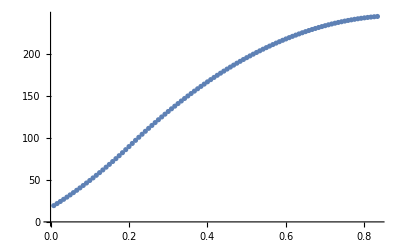

```mathematica
ListPlot[data[[All, {1,2}]]]
```

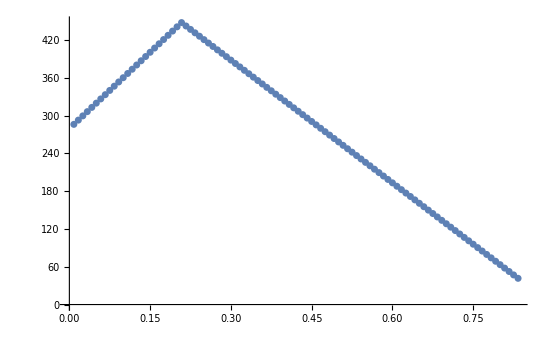

```mathematica
ListPlot[data[[All, {1,3}]]]
```

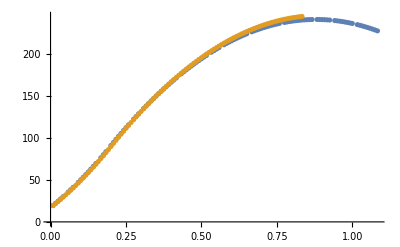

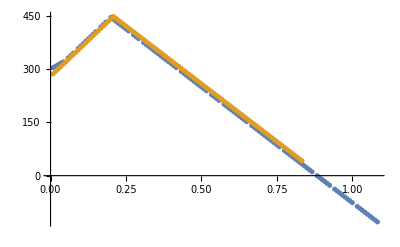

```mathematica
range = 35;;150;
t0 = t[[range[[1]]-1]];
ListPlot[{
Transpose[{t[[range]]-t0, x[[range]]}],
data[[All, {1,2}]]
}]
ListPlot[{
Transpose[{t[[range]]-t0, v[[range]]}],
data[[All, {1,3}]]
}]
```